1th iteration value is :3/2

Estimated error in 1 th iteration is: 1/2

2th iteration value is :5/4

Estimated error in 2 th iteration is: 1/4

3th iteration value is :11/8

Estimated error in 3 th iteration is: 1/8

4th iteration value is :23/16

Estimated error in 4 th iteration is: 1/16

5th iteration value is :47/32

Estimated error in 5 th iteration is: 1/32

6th iteration value is :95/64

Estimated error in 6 th iteration is: 1/64

The approximate root is :1.48438

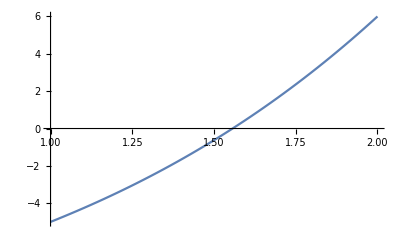

```mathematica
f[x_]:= x^3+4x-10;
a=1;
b=2;
e = 0.01;
Nmax = 6;
If[f[a]*f[b]>0,
Print["These values do not satisfy the IVP so change the initial value"],
	For[i=1,i<=Nmax,i++,c=(a+b)/2;
	If[Abs[(b-a)/2]<e,Return[c],
	Print[i,"th iteration value is :",c];
	Print["Estimated error in ",i," th iteration is: ",(b-a)/2];
If[f[a]*f[b]<0,b=c,a=c]]]];
Print["The approximate root is :",N[c]];
Plot[f[x],{x,1,2}]
```

1th iteration value is :1

Estimated error in 1 th iteration is: 1

2th iteration value is :1/2

Estimated error in 2 th iteration is: 1/2

3th iteration value is :3/4

Estimated error in 3 th iteration is: 1/4

4th iteration value is :7/8

Estimated error in 4 th iteration is: 1/8

5th iteration value is :15/16

Estimated error in 5 th iteration is: 1/16

6th iteration value is :31/32

Estimated error in 6 th iteration is: 1/32

7th iteration value is :63/64

Estimated error in 7 th iteration is: 1/64

8th iteration value is :127/128

Estimated error in 8 th iteration is: 1/128

9th iteration value is :255/256

Estimated error in 9 th iteration is: 1/256

10th iteration value is :511/512

Estimated error in 10 th iteration is: 1/512

The approximate root is :0.998047

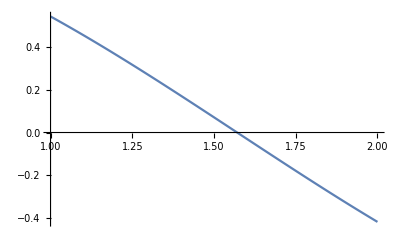

```mathematica
f[x_]:= Cos[x];
a=0;
b=2;
e = 0.001;
Nmax = 11;
If[f[a]*f[b]>0,
Print["These values do not satisfy the IVP so change the initial value"],
	For[i=1,i<Nmax,i++,c=(a+b)/2;
	If[Abs[(b-a)/2]<e,Return[c],
	Print[i,"th iteration value is :",c];
	Print["Estimated error in ",i," th iteration is: ",(b-a)/2];
If[f[a]*f[b]<0,b=c,a=c]]]];
Print["The approximate root is :",N[c]];
Plot[f[x],{x,1,2}]
```

1th iteration value is :π/2

Estimated error in 1 th iteration is: π/2

2th iteration value is :(3 π)/4

Estimated error in 2 th iteration is: π/4

3th iteration value is :(7 π)/8

Estimated error in 3 th iteration is: π/8

4th iteration value is :(15 π)/16

Estimated error in 4 th iteration is: π/16

5th iteration value is :(31 π)/32

Estimated error in 5 th iteration is: π/32

6th iteration value is :(63 π)/64

Estimated error in 6 th iteration is: π/64

7th iteration value is :(127 π)/128

Estimated error in 7 th iteration is: π/128

8th iteration value is :(255 π)/256

Estimated error in 8 th iteration is: π/256

9th iteration value is :(511 π)/512

Estimated error in 9 th iteration is: π/512

10th iteration value is :(1023 π)/1024

Estimated error in 10 th iteration is: π/1024

11th iteration value is :(2047 π)/2048

Estimated error in 11 th iteration is: π/2048

The approximate root is :3.14006

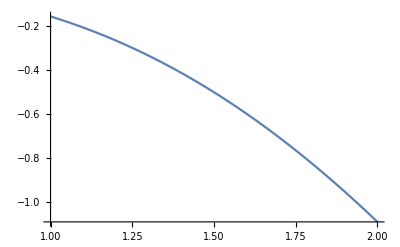

```mathematica
f[x_]:=  Sin[x]-x;
a=0;
b=Pi;
e = 0.001;
Nmax = 11;
If[f[a]*f[b]>0,
Print["These values do not satisfy the IVP so change the initial value"],
	For[i=1,i<=Nmax,i++,c=(a+b)/2;
	If[Abs[(b-a)/2]<e,Return[c],
	Print[i,"th iteration value is :",c];
	Print["Estimated error in ",i," th iteration is: ",(b-a)/2];
If[f[a]*f[b]<0,b=c,a=c]]]];
Print["The approximate root is :",N[c]];
Plot[f[x],{x,1,2}]
```

These values do not satisfy the IVP so change the initial value

The approximate root is :3.09251

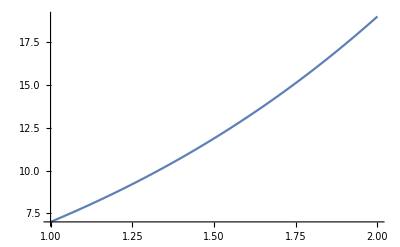

```mathematica
f[x_]:= x^3+5x+1;
a=0;
b=1;
e = 0.001;
Nmax = 6;
If[f[a]*f[b]>0,
Print["These values do not satisfy the IVP so change the initial value"],
	For[i=1,i<Nmax,i++,c=(a+b)/2;
	If[Abs[(b-a)/2]<e,Return[c],
	Print[i,"th iteration value is :",c];
	Print["Estimated error in ",i," th iteration is: ",(b-a)/2];
If[f[a]*f[b]<0,b=c,a=c]]]];
Print["The approximate root is :",N[c]];
Plot[f[x],{x,1,2}]
```

1th iteration value is :0.44

Estimated error in 1 th iteration is: 0.04

2th iteration value is :0.42

Estimated error in 2 th iteration is: 0.02

3th iteration value is :0.43

Estimated error in 3 th iteration is: 0.01

Return[0.435]

The approximate root is :0.435

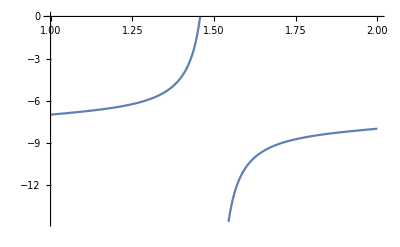

```mathematica
f[x_]:= Tan[Pi x]-x-6;
a=0.4;
b=0.48;
e = 0.01;
Nmax = 6;
If[f[a]*f[b]>0,
Print["These values do not satisfy the IVP so change the initial value"],
	For[i=1,i<=Nmax,i++,c=(a+b)/2;
	If[Abs[(b-a)/2]<e,Return[c],
	Print[i,"th iteration value is :",c];
	Print["Estimated error in ",i," th iteration is: ",(b-a)/2];
If[f[a]*f[b]<0,b=c,a=c]]]];
Print["The approximate root is :",N[c]];
Plot[f[x],{x,1,2}]
```